# Local Tidal Tensor via ZAMO

## A Fully General Approach for Spherical Spacetimes (with Tests)

```mathematica
ClearAll["`*"](* reset ALL variables of this notebook context *)
```

## 0. Define Helper Functions

### Code for optimising symbolic expressions to C++

ref. https://github.com/ABHModels/raytransfer

```mathematica
(*::Package::*)

BeginPackage["OptimizeExpressionToC`"];

OptimizeExpressionToC::usage="Generates optimized version of expression in C";

ExtractTags::usage="";
ClearTagText::usage="";
TagExistQ::usage="";
AppendToTag::usage="";

Begin["Private`"];

OptimizeExpressionToC[expr_List]:=Module[{optimizedExpr,mainExpr,n,m,defs,output},optimizedExpr=Experimental`OptimizeExpression[expr];If[ToString@optimizedExpr[[1,0]]=="Block",{n=Length[optimizedExpr[[1,1]]];mainExpr=optimizedExpr[[1,2,n+1]];},{n=0;mainExpr=Flatten@{optimizedExpr[[1]]};}];m=Length[mainExpr];defs=Table["double "<>ToString@CForm@optimizedExpr[[1,2,i,1]]<>" = "<>ToString@CForm@optimizedExpr[[1,2,i,2]]<>";",{i,1,n}];output=MapIndexed["out("<>StringJoin@Riffle[ToString/@(#2-1),""]<>") = "<>ToString@CForm@#1<>";"&,mainExpr,{ArrayDepth[mainExpr]}];StringReplace[Join[defs,output],"Compile_$"->"t"]];

End[];
Null

ExtractTags[string_String]:=Module[{regex,extractTag},regex=RegularExpression["\\n([^\\n]*)// (\\[|</?)([^\\]\\n]*)(\\]|>)[^\\n]*\\n"];extractTag[bounds_]:=Module[{substring,indentation,tagType,tag},substring=StringTake[string,bounds];{{indentation,tagType,tag}}=StringCases[substring,regex->{"$1","$2","$3"}];Association["indentation"->indentation,"tagType"->tagType,"tag"->tag,"start"->bounds[[1]]+1,"end"->bounds[[2]]]];extractTag[#]&/@StringPosition[string,regex]];

TagExistQ[string_String,tag_String]:=AnyTrue[ExtractTags[string],#[["tag"]]==tag&];

ClearTagText[string_String,tag_String]:=Module[{tags,startTag,endTag,x},tags=ExtractTags[string];startTag=FirstCase[tags,x_/;x[["tag"]]==tag&&x[["tagType"]]=="<"];endTag=FirstCase[tags,x_/;x[["tag"]]==tag&&x[["tagType"]]=="</"];StringTake[string,{1,startTag[["end"]]}]<>StringTake[string,{endTag[["start"]],StringLength[string]}]]

AppendToTag[string_String,tag_String,linesToAppend_List]:=Module[{tags,startTag,indent,x},tags=ExtractTags[string];startTag=FirstCase[tags,x_/;x[["tag"]]==tag&&x[["tagType"]]=="<"];indent=startTag[["indentation"]];StringTake[string,{1,startTag[["end"]]}]<>StringRiffle[linesToAppend,{indent,"\n"<>indent,"\n"}]<>StringTake[string,{startTag[["end"]]+1,StringLength[string]}]];

AppendToTag[string_String,tag_String,stringToAppend_String]:=AppendToTag[string,tag,StringSplit[stringToAppend,"\n"]];
Null

EndPackage[];
```

```mathematica
outputMetric[matrix_,filename_:"metric.cpp"]:=Module[{text,meat,header,footer,output},text=OptimizeExpressionToC[{matrix[[1]][[1]],matrix[[1]][[2]],matrix[[1]][[3]],matrix[[1]][[4]],matrix[[2]][[1]],matrix[[2]][[2]],matrix[[2]][[3]],matrix[[2]][[4]],matrix[[3]][[1]],matrix[[3]][[2]],matrix[[3]][[3]],matrix[[3]][[4]],matrix[[4]][[1]],matrix[[4]][[2]],matrix[[4]][[3]],matrix[[4]][[4]]}];
meat=ToString[Column[StringReplace[text,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow","Sin"->"sin","Cos"->"cos","Csc"->"1/sin","Cot"->"1/tan","double"->"double",";,"->";\n    ","out(0)"->"g[0][0]","out(1)"->"g[0][1]","out(2)"->"g[0][2]","out(3)"->"g[0][3]","out(4)"->"g[1][0]","out(5)"->"g[1][1]","out(6)"->"g[1][2]","out(7)"->"g[1][3]","out(8)"->"g[2][0]","out(9)"->"g[2][1]","out(10)"->"g[2][2]","out(11)"->"g[2][3]","out(12)"->"g[3][0]","out(13)"->"g[3][1]","out(14)"->"g[3][2]","out(15)"->"g[3][3]"}]]];
header="void metric(double r, double chi, double g[4][4])\n{\n";
footer="\n}";
output=header<>meat<>footer;
Export[filename,output,"Text"]]

outputChristoffel[matrix_,filename_:"christoffel.cpp"]:=Module[{text,meat,header,footer,output},text=OptimizeExpressionToC[{matrix[[1]][[1]][[1]],matrix[[1]][[1]][[2]],matrix[[1]][[1]][[3]],matrix[[1]][[1]][[4]],matrix[[1]][[2]][[1]],matrix[[1]][[2]][[2]],matrix[[1]][[2]][[3]],matrix[[1]][[2]][[4]],matrix[[1]][[3]][[1]],matrix[[1]][[3]][[2]],matrix[[1]][[3]][[3]],matrix[[1]][[3]][[4]],matrix[[1]][[4]][[1]],matrix[[1]][[4]][[2]],matrix[[1]][[4]][[3]],matrix[[1]][[4]][[4]],matrix[[2]][[1]][[1]],matrix[[2]][[1]][[2]],matrix[[2]][[1]][[3]],matrix[[2]][[1]][[4]],matrix[[2]][[2]][[1]],matrix[[2]][[2]][[2]],matrix[[2]][[2]][[3]],matrix[[2]][[2]][[4]],matrix[[2]][[3]][[1]],matrix[[2]][[3]][[2]],matrix[[2]][[3]][[3]],matrix[[2]][[3]][[4]],matrix[[2]][[4]][[1]],matrix[[2]][[4]][[2]],matrix[[2]][[4]][[3]],matrix[[2]][[4]][[4]],matrix[[3]][[1]][[1]],matrix[[3]][[1]][[2]],matrix[[3]][[1]][[3]],matrix[[3]][[1]][[4]],matrix[[3]][[2]][[1]],matrix[[3]][[2]][[2]],matrix[[3]][[2]][[3]],matrix[[3]][[2]][[4]],matrix[[3]][[3]][[1]],matrix[[3]][[3]][[2]],matrix[[3]][[3]][[3]],matrix[[3]][[3]][[4]],matrix[[3]][[4]][[1]],matrix[[3]][[4]][[2]],matrix[[3]][[4]][[3]],matrix[[3]][[4]][[4]],matrix[[4]][[1]][[1]],matrix[[4]][[1]][[2]],matrix[[4]][[1]][[3]],matrix[[4]][[1]][[4]],matrix[[4]][[2]][[1]],matrix[[4]][[2]][[2]],matrix[[4]][[2]][[3]],matrix[[4]][[2]][[4]],matrix[[4]][[3]][[1]],matrix[[4]][[3]][[2]],matrix[[4]][[3]][[3]],matrix[[4]][[3]][[4]],matrix[[4]][[4]][[1]],matrix[[4]][[4]][[2]],matrix[[4]][[4]][[3]],matrix[[4]][[4]][[4]]}];
meat=ToString[Column[StringReplace[text,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow","Sin"->"sin","Cos"->"cos","Csc"->"1/sin","Cot"->"1/tan","double"->"double",";,"->";\n    ","out(0)"->"christ[0][0][0]","out(1)"->"christ[0][0][1]","out(2)"->"christ[0][0][2]","out(3)"->"christ[0][0][3]","out(4)"->"christ[0][1][0]","out(5)"->"christ[0][1][1]","out(6)"->"christ[0][1][2]","out(7)"->"christ[0][1][3]","out(8)"->"christ[0][2][0]","out(9)"->"christ[0][2][1]","out(10)"->"christ[0][2][2]","out(11)"->"christ[0][2][3]","out(12)"->"christ[0][3][0]","out(13)"->"christ[0][3][1]","out(14)"->"christ[0][3][2]","out(15)"->"christ[0][3][3]","out(16)"->"christ[1][0][0]","out(17)"->"christ[1][0][1]","out(18)"->"christ[1][0][2]","out(19)"->"christ[1][0][3]","out(20)"->"christ[1][1][0]","out(21)"->"christ[1][1][1]","out(22)"->"christ[1][1][2]","out(23)"->"christ[1][1][3]","out(24)"->"christ[1][2][0]","out(25)"->"christ[1][2][1]","out(26)"->"christ[1][2][2]","out(27)"->"christ[1][2][3]","out(28)"->"christ[1][3][0]","out(29)"->"christ[1][3][1]","out(30)"->"christ[1][3][2]","out(31)"->"christ[1][3][3]","out(32)"->"christ[2][0][0]","out(33)"->"christ[2][0][1]","out(34)"->"christ[2][0][2]","out(35)"->"christ[2][0][3]","out(36)"->"christ[2][1][0]","out(37)"->"christ[2][1][1]","out(38)"->"christ[2][1][2]","out(39)"->"christ[2][1][3]","out(40)"->"christ[2][2][0]","out(41)"->"christ[2][2][1]","out(42)"->"christ[2][2][2]","out(43)"->"christ[2][2][3]","out(44)"->"christ[2][3][0]","out(45)"->"christ[2][3][1]","out(46)"->"christ[2][3][2]","out(47)"->"christ[2][3][3]","out(48)"->"christ[3][0][0]","out(49)"->"christ[3][0][1]","out(50)"->"christ[3][0][2]","out(51)"->"christ[3][0][3]","out(52)"->"christ[3][1][0]","out(53)"->"christ[3][1][1]","out(54)"->"christ[3][1][2]","out(55)"->"christ[3][1][3]","out(56)"->"christ[3][2][0]","out(57)"->"christ[3][2][1]","out(58)"->"christ[3][2][2]","out(59)"->"christ[3][2][3]","out(60)"->"christ[3][3][0]","out(61)"->"christ[3][3][1]","out(62)"->"christ[3][3][2]","out(63)"->"christ[3][3][3]"}]]];
header="void christoffel(double r, double chi, double christ[4][4][4])\n{\n";
footer="\n}";
output=header<>meat<>footer;
Export[filename,output,"Text"]]

outputTidal[matrix_,filename_:"Cloc.cpp"]:=Module[{text,meat,header,footer,output},text=OptimizeExpressionToC[{matrix[[1]][[1]],matrix[[1]][[2]],matrix[[1]][[3]],matrix[[1]][[4]],matrix[[2]][[1]],matrix[[2]][[2]],matrix[[2]][[3]],matrix[[2]][[4]],matrix[[3]][[1]],matrix[[3]][[2]],matrix[[3]][[3]],matrix[[3]][[4]],matrix[[4]][[1]],matrix[[4]][[2]],matrix[[4]][[3]],matrix[[4]][[4]]}];
meat=ToString[Column[StringReplace[text,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow","Abs"->"abs","Sin"->"sin","Cos"->"cos","Csc"->"1/sin","Cot"->"1/tan",";,"->";\n    ","double"->"complex<double>","out(0)"->"C[0][0]","out(1)"->"C[0][1]","out(2)"->"C[0][2]","out(3)"->"C[0][3]","out(4)"->"C[1][0]","out(5)"->"C[1][1]","out(6)"->"C[1][2]","out(7)"->"C[1][3]","out(8)"->"C[2][0]","out(9)"->"C[2][1]","out(10)"->"C[2][2]","out(11)"->"C[2][3]","out(12)"->"C[3][0]","out(13)"->"C[3][1]","out(14)"->"C[3][2]","out(15)"->"C[3][3]"}]]];
header="void ClocH(complex<double> M, complex<double> a, complex<double> Q, complex<double> e, complex<double> lz, complex<double> ep, complex<double> q, complex<double> r, complex<double> theta, complex<double> dt, complex<double> dr, complex<double> dtheta, complex<double> dphi, complex<double> C[4][4])\n{\n";
footer="\n}";
output=header<>meat<>footer;
Export[filename,output,"Text"]]
```

### Functions for solving IBSO radii

```mathematica
expr[chi_,Q_]:=chi^3-4*chi^2+4*Q^2*chi-Q^4;
momentum[chi_, Q_]:=Sqrt[(2*chi^3-(Q*chi)^2)/(chi^2-2*chi+Q^2)];
chisol[Q_]:=Module[{charge=Q,temp,out,x},
out =Max[x/.NSolve[expr[x,charge]==0&&x>0,x,Reals,WorkingPrecision->16]];
out
];
```

### Modules for constructing tensors

```mathematica
getR[a0_,b0_,c0_,d0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,For[k0=1,k0<=4,k0++,For[l0=1,l0<=4,l0++,component+=Part[Robs,i0,j0,k0,l0]*Part[matdown,a0,i0]*Part[matdown,b0,j0]*Part[matdown,c0,k0]*Part[matdown,d0,l0];]]]];
component]

getRH[a0_,b0_,c0_,d0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,component+=Part[Rlnrf,i0,b0,c0,d0]*Part[eta,a0,i0];];
component]

getRIC[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component+=Part[eta,i0,j0]*Part[Rlnrf,i0,a0,j0,b0];]];
component]

getRlocH[a0_,b0_,c0_,d0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,For[k0=1,k0<=4,k0++,For[l0=1,l0<=4,l0++,component+=Part[RlnrfH,i0,j0,k0,l0]*Part[lorentz,a0,i0]*Part[lorentzinv,j0,b0]*Part[lorentzinv,k0,c0]*Part[lorentzinv,l0,d0];]]]];
component]

getC[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[Rlnrf,a0,i0,b0,j0]*Part[Ulnrf,i0]*Part[Ulnrf,j0];]];
component]

getCH[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[RlnrfH,a0,i0,b0,j0]*Part[Ulnrf,i0]*Part[Ulnrf,j0];]];
component]

getCobs[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[Robs,a0,i0,b0,j0]*Part[U,i0]*Part[U,j0];]];
component]

getCobsH[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[RobsH,a0,i0,b0,j0]*Part[U,i0]*Part[U,j0];]];
component]

getClocH[mu0_,nu0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component+=Part[ClnrfH,i0,j0]*Part[lorentz,mu0,i0]*Part[lorentzinv,j0,nu0];]];
component]

genRlnrf[]:=Module[{i0,j0,k0,l0,output},output=Table[getR[i0,j0,k0,l0],{i0,1,4},{j0,1,4},{k0,1,4},{l0,1,4}];
Simplify[output,Assumptions->assume]]

genRlnrfH[]:=Module[{i0,j0,k0,l0,output},output=Table[getRH[i0,j0,k0,l0],{i0,1,4},{j0,1,4},{k0,1,4},{l0,1,4}];
Simplify[output,Assumptions->assume]]

genRIClnrf[]:=Module[{i0,j0,output},output=Table[getRIC[i0,j0],{i0,1,4},{j0,1,4}];
Simplify[output,Assumptions->assume]]

genUlnrf[]:=Module[{i0,j0,output},output=ConstantArray[0,{4}];
For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,output[[i0]]+=Part[U,j0]*Part[matup,i0,j0];]];
Simplify[output,Assumptions->assume]]

genClnrf[]:=Module[{i0,j0,output},output=Table[getC[i0,j0],{i0,1,4},{j0,1,4}];
-output]

genClnrfH[]:=Module[{i0,j0,output},output=Table[getCH[i0,j0],{i0,1,4},{j0,1,4}];
-output]

genCobs[]:=Module[{i0,j0,output},output=Table[getCobs[i0,j0],{i0,1,4},{j0,1,4}];
-output]

genCobsH[]:=Module[{i0,j0,output},output=Table[getCobsH[i0,j0],{i0,1,4},{j0,1,4}];
-output]

genClocH[]:=Module[{i0,j0,output},output=Table[getClocH[i0,j0],{i0,1,4},{j0,1,4}];
output]

genRlocH[]:=Module[{i0,j0,k0,l0,output},output=Table[getRlocH[i0,j0,k0,l0],{i0,1,4},{j0,1,4},{k0,1,4},{l0,1,4}];
output]

genLorentz[]:=Module[{i0,j0,output,beta,gamma,betar,betatheta,betaphi},beta=Sqrt[Part[UlnrfN,2]^2+Part[UlnrfN,3]^2+Part[UlnrfN,4]^2];
gamma=1/Sqrt[1-beta^2];
betar=Part[UlnrfN,2];
betatheta=Part[UlnrfN,3];
betaphi=Part[UlnrfN,4];
output={{gamma,-gamma*betar,-gamma*betatheta,-gamma*betaphi},{-gamma*betar,1+(gamma-1)*betar^2/(beta^2),(gamma-1)*betar*betatheta/(beta^2),(gamma-1)*betar*betaphi/(beta^2)},{-gamma*betatheta,(gamma-1)*betar*betatheta/(beta^2),1+(gamma-1)*betatheta^2/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2)},{-gamma*betaphi,(gamma-1)*betar*betaphi/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2),1+(gamma-1)*betaphi^2/(beta^2)}};
output]

genLorentzinv[]:=Module[{i0,j0,output,beta,gamma,betar,betatheta,betaphi},beta=Sqrt[Part[UlnrfN,2]^2+Part[UlnrfN,3]^2+Part[UlnrfN,4]^2];
gamma=1/Sqrt[1-beta^2];
betar=Part[UlnrfN,2];
betatheta=Part[UlnrfN,3];
betaphi=Part[UlnrfN,4];
output={{gamma,gamma*betar,gamma*betatheta,gamma*betaphi},{gamma*betar,1+(gamma-1)*betar^2/(beta^2),(gamma-1)*betar*betatheta/(beta^2),(gamma-1)*betar*betaphi/(beta^2)},{gamma*betatheta,(gamma-1)*betar*betatheta/(beta^2),1+(gamma-1)*betatheta^2/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2)},{gamma*betaphi,(gamma-1)*betar*betaphi/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2),1+(gamma-1)*betaphi^2/(beta^2)}};
output]
```

## 1. Construct Metric and LNRF Tetrad

### Define Metric Functions (general spherical)

```mathematica
Clear[A,B,Cfunc];
tt=A[r];
rr=B[r];
thth=Cfunc[r];

nu = Log[tt]/ 2;

psi = Log[thth*(Sin[theta])^2] / 2;

mu1 = Log[rr] / 2;

mu2 = Log[thth] / 2;

omega =0;

assume = { M >0, r >0,  0<theta<Pi/2 ,ep>0,A[r]>0,B[r]>0,Cfunc[r]>0};
```

First integrals to geodesic equations

```mathematica
dsub = {dt -> ep/A[r],
 dr -> Sqrt[(ep^2/A[r]-lz^2/Cfunc[r]-1)/B[r]], 
dtheta -> 0, 
dphi -> lz/((r)^2)
};
```

### Construct metric

```mathematica
g00 = -Exp[2 * nu] + omega^2 * Exp[2 * psi];

g11 = Exp[2 * mu1];

g22 = Exp[2 * mu2];

g33 = Exp[2 * psi];

g03 = -omega * Exp[2 * psi];

g30 = g03;

G = Simplify[{{g00, 0, 0, g03}, {0, g11, 0, 0}, {0, 0, g22, 0}, {g03,
     0, 0, g33}}];

G // MatrixForm
eta = {{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
Ginv = Simplify[Inverse[G],Assumptions->assume];
Ginv // MatrixForm
eta//MatrixForm
```

(-A[r] | 0 | 0 | 0
0 | B[r] | 0 | 0
0 | 0 | Cfunc[r] | 0
0 | 0 | 0 | Cfunc[r] Sin[theta]^2)

(-1/A[r] | 0 | 0 | 0
0 | 1/B[r] | 0 | 0
0 | 0 | 1/Cfunc[r] | 0
0 | 0 | 0 | Csc[theta]^2/Cfunc[r])

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

### Construct LNRF tetrad

```mathematica
etup = {Exp[nu], 0, 0, 0};

erup = {0, Exp[mu1], 0, 0};

ethetaup = {0, 0, Exp[mu2], 0};

ephiup = {-omega * Exp[psi], 0, 0, Exp[psi]};

etdown = {Exp[-nu], 0, 0, omega * Exp[-nu]};

erdown = {0, Exp[-mu1], 0, 0};

ethetadown = {0, 0, Exp[-mu2], 0};

ephidown = {0, 0, 0, Exp[-psi]};

matup = Simplify[{etup, erup, ethetaup, ephiup}, Assumptions -> assume
    ];

matdown = Simplify[{etdown, erdown, ethetadown, ephidown}, Assumptions
     -> assume];

matup //MatrixForm
matdown //MatrixForm
```

(√A[r] | 0 | 0 | 0
0 | √B[r] | 0 | 0
0 | 0 | √Cfunc[r] | 0
0 | 0 | 0 | √Cfunc[r] Sin[theta])

(1/(√A[r]) | 0 | 0 | 0
0 | 1/(√B[r]) | 0 | 0
0 | 0 | 1/(√Cfunc[r]) | 0
0 | 0 | 0 | Csc[theta]/(√Cfunc[r]))

```mathematica
zeta=omega;
sig=Simplify[1/Sqrt[-g00-2*zeta*g03-zeta*zeta*g33],Assumptions->assume];
del=Simplify[1/Sqrt[g03*g03-g00*g33], Assumptions->assume];

etdown = {temp, 0, 0,temp*zeta};

erdown = {0, 1/Sqrt[g11], 0, 0};

ethetadown = {0, 0, 1/Sqrt[g22], 0};

ephidown ={temp*del*(g03+zeta*g33), 0, 0, -temp*del*( g00+zeta*g03)};


matdown = FullSimplify[{etdown, erdown, ethetadown, ephidown}, Assumptions
     -> assume];

matup = FullSimplify[Transpose[Inverse[matdown]],Assumptions->assume];

matup //MatrixForm
matdown //MatrixForm

FullSimplify[matup.Transpose[matdown],Assumptions->assume]//MatrixForm
```

(1/temp | 0 | 0 | 0
0 | √B[r] | 0 | 0
0 | 0 | √Cfunc[r] | 0
0 | 0 | 0 | (√(Cfunc[r]/A[r]) Sin[theta])/temp)

(temp | 0 | 0 | 0
0 | 1/(√B[r]) | 0 | 0
0 | 0 | 1/(√Cfunc[r]) | 0
0 | 0 | 0 | temp √(A[r]/Cfunc[r]) Csc[theta])

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## 2. Compute Riemann Tensors in LNRF

### Riemann tensor in observer frame

last two lines take quite a while

```mathematica
metric = ResourceFunction["MetricTensor"][G, {t, r, theta, phi}, True,
     True];

riemann = ResourceFunction["RiemannTensor"][metric];

riemann2 = riemann["CovariantRiemannTensor"];

AbsoluteTiming[
Robs = riemann2["ReducedTensorRepresentation"];
RobsH=riemann["ReducedTensorRepresentation"];
]
(*ricci=ResourceFunction["RicciTensor"][metric]
ricci["ReducedMatrixRepresentation"];
ricci["RicciScalar"]//Simplify*)
```

{0.486538,Null}

### Riemann and Ricci tensors in LNRF

```mathematica
Rlnrf=genRlnrf[];
RlnrfH=genRlnrfH[];
RIClnrf=genRIClnrf[];
```

Check Ricci flatness

```mathematica
FullSimplify[RIClnrf/.{M->1}, Assumptions->assume] // MatrixForm
```

((-A'[r] (A[r] Cfunc[r] B'[r]+B[r] (Cfunc[r] A'[r]-2 A[r] Cfunc'[r]))+2 A[r] B[r] Cfunc[r] A''[r])/(4 A[r]^2 B[r]^2 Cfunc[r]) | 0 | 0 | 0
0 | ((A[r] A'[r] B'[r]+B[r] (A'[r]^2-2 A[r] A''[r]))/A[r]^2+(2 (B[r] Cfunc'[r]^2+Cfunc[r] (B'[r] Cfunc'[r]-2 B[r] Cfunc''[r])))/Cfunc[r]^2)/(4 B[r]^2) | 0 | 0
0 | 0 | (-B[r] A'[r] Cfunc'[r]+A[r] (4 B[r]^2+B'[r] Cfunc'[r]-2 B[r] Cfunc''[r]))/(4 A[r] B[r]^2 Cfunc[r]) | 0
0 | 0 | 0 | (-B[r] A'[r] Cfunc'[r]+A[r] (4 B[r]^2+B'[r] Cfunc'[r]-2 B[r] Cfunc''[r]))/(4 A[r] B[r]^2 Cfunc[r]))

### Velocity vector in LNRF

```mathematica
U = {dt, dr, dtheta, dphi};

Ulnrf=genUlnrf[];
Ulnrf //MatrixForm

UlnrfN =Simplify [Ulnrf/Part[Ulnrf,1],Assumptions->assume];
UlnrfN//MatrixForm
```

(dt √A[r]
dr √B[r]
dtheta √Cfunc[r]
dphi √Cfunc[r] Sin[theta])

(1
(dr √(B[r]/A[r]))/dt
(dtheta √(Cfunc[r]/A[r]))/dt
(dphi √(Cfunc[r]/A[r]) Sin[theta])/dt)

## 3. Compute Tidal Tensors and Test

### Tidal tensor in different frames

```mathematica
Clnrf=genClnrf[];
ClnrfH=genClnrfH[];
Cobs=genCobs[];
CobsH=genCobsH[];
```

Lorentz boost to local free falling frame to get local tensor

```mathematica
lorentz = genLorentz[];
lorentzinv=genLorentzinv[];
ClocH = genClocH[];
```

```mathematica
RlocH=genRlocH[];
ClocHalt=Table[Part[RlocH,i0,1,j0,1],{i0,1,4},{j0,1,4}];
```

Check determinant of tidal tensors

```mathematica
test=Det[ClocHalt]/.dsub;
Simplify[test/.{M->1},Assumptions->assume]
```

0

Check trace of tidal tensors

```mathematica
test=Tr[ClocH]/.dsub;
FullSimplify[test,Assumptions->assume]
```

-1/(4 r^4 A[r]^2 B[r]^2 Cfunc[r]^3)(r^4 B[r] Cfunc[r]^2 A'[r] ((lz^2+Cfunc[r]) A'[r]-2 ep^2 Cfunc'[r])+A[r] Cfunc[r] (-2 ep^2 r^4 B[r] Cfunc'[r]^2+Cfunc[r]^2 (A'[r] (r^4 B'[r]+lz^2 B[r] Sin[theta]^2 Cfunc'[r])-2 r^4 B[r] A''[r])+r^4 Cfunc[r] (lz^2 A'[r] B'[r]-2 ep^2 B'[r] Cfunc'[r]-2 lz^2 B[r] A''[r]+4 ep^2 B[r] Cfunc''[r]))+A[r]^2 (-4 lz^2 B[r]^2 Cfunc[r]^3 Sin[theta]^2+Cfunc[r] (2 r^4 (lz^2+Cfunc[r])-lz^2 Cfunc[r]^2 Sin[theta]^2) B'[r] Cfunc'[r]+2 B[r] (r^4 (lz^2+Cfunc[r]) Cfunc'[r]^2+Cfunc[r] (-2 r^4 (lz^2+Cfunc[r])+lz^2 Cfunc[r]^2 Sin[theta]^2) Cfunc''[r])))

```mathematica
test=Tr[ClocHalt]/.dsub;
Simplify[test,Assumptions->assume]
```

(r^4 B[r] Cfunc[r]^2 A'[r] ((lz^2+Cfunc[r]) A'[r]-2 ep^2 Cfunc'[r])+A[r] Cfunc[r] (-2 ep^2 r^4 B[r] Cfunc'[r]^2+Cfunc[r]^2 (A'[r] (r^4 B'[r]+lz^2 B[r] Sin[theta]^2 Cfunc'[r])-2 r^4 B[r] A''[r])+r^4 Cfunc[r] (lz^2 A'[r] B'[r]-2 ep^2 B'[r] Cfunc'[r]-2 lz^2 B[r] A''[r]+4 ep^2 B[r] Cfunc''[r]))+A[r]^2 (-4 lz^2 B[r]^2 Cfunc[r]^3 Sin[theta]^2+Cfunc[r] (2 lz^2 r^4+2 r^4 Cfunc[r]-lz^2 Cfunc[r]^2 Sin[theta]^2) B'[r] Cfunc'[r]+2 B[r] (r^4 (lz^2+Cfunc[r]) Cfunc'[r]^2+Cfunc[r] (-2 lz^2 r^4-2 r^4 Cfunc[r]+lz^2 Cfunc[r]^2 Sin[theta]^2) Cfunc''[r])))/(4 A[r]^2 B[r]^2 Cfunc[r]^2 (-lz^2 r^4-r^4 Cfunc[r]+lz^2 Cfunc[r]^2 Sin[theta]^2))

```mathematica
reduced=ClocH/.dsub;
reducedalt=ClocHalt/.dsub;
```

```mathematica
Clear[A,B,Cfunc]
Cfunc[r_]=r^2;
assume = { M >0, r >0,  0<theta<Pi/2 ,ep>0,A[r]>0,B[r]>0,Cfunc[r]>0};
testmat = Simplify[reducedalt/.{M->1,theta->Pi/2},Assumptions->assume];
testmat//MatrixForm
```

(0 | 0 | 0 | 0
0 | -(ep^2 r^5 B[r] A'[r]^2+2 ep r^3 (lz^2+r^2) √A[r] B[r] A'[r]^2-4 ep lz^2 r^2 A[r]^(5/2) B'[r]-2 lz^2 r^2 A[r]^3 B'[r]+2 ep r^3 (lz^2+r^2) A[r]^(3/2) (A'[r] B'[r]-2 B[r] A''[r])+A[r] (ep^2 r^5 A'[r] B'[r]+r B[r] (-2 ep^2 lz^2 r A'[r]+(lz^2+r^2)^2 A'[r]^2-2 ep^2 r^4 A''[r]))+A[r]^2 (r (-2 ep^2 lz^2 r+(lz^2+r^2)^2 A'[r]) B'[r]-2 (lz^2+r^2) B[r] (-lz^2 A'[r]+r (lz^2+r^2) A''[r])))/(4 r^5 (ep+√A[r])^2 A[r]^2 B[r]^2) | 0 | -(lz √(ep^2 r^2-(lz^2+r^2) A[r]) (-ep r^3 B[r] A'[r]^2-r √A[r] B[r] A'[r] (-2 ep^2 r+(lz^2+r^2) A'[r])+4 ep r^2 A[r]^2 B'[r]+2 r^2 A[r]^(5/2) B'[r]+ep r^2 A[r] (-r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))-A[r]^(3/2) (r (-2 ep^2 r+(lz^2+r^2) A'[r]) B'[r]+2 B[r] (lz^2 A'[r]-r (lz^2+r^2) A''[r]))))/(4 r^5 (ep+√A[r])^2 A[r]^2 B[r]^2)
0 | 0 | (ep^2 r^3 B[r] A'[r]+ep^2 r^3 A[r] B'[r]+A[r]^2 (-2 lz^2 B[r]+2 lz^2 B[r]^2-r (lz^2+r^2) B'[r]))/(2 r^4 A[r]^2 B[r]^2) | 0
0 | -(lz √(ep^2 r^2-(lz^2+r^2) A[r]) (-ep r^3 B[r] A'[r]^2-r √A[r] B[r] A'[r] (-2 ep^2 r+(lz^2+r^2) A'[r])+4 ep r^2 A[r]^2 B'[r]+2 r^2 A[r]^(5/2) B'[r]+ep r^2 A[r] (-r A'[r] B'[r]+2 B[r] (A'[r]+r A''[r]))-A[r]^(3/2) (r (-2 ep^2 r+(lz^2+r^2) A'[r]) B'[r]+2 B[r] (lz^2 A'[r]-r (lz^2+r^2) A''[r]))))/(4 r^5 (ep+√A[r])^2 A[r]^2 B[r]^2) | 0 | ((ep-√A[r])^2 (r A[r] (ep^2 r^2-(lz^2+r^2) A[r]) (2 ep^2 r+4 ep r √A[r]+2 r A[r]-lz^2 A'[r]) B'[r]+B[r] (2 (ep^2 r^2+ep r^2 √A[r]-lz^2 A[r])^2 A'[r]+lz^2 r (-ep^2 r^2+(lz^2+r^2) A[r]) A'[r]^2-2 lz^2 r A[r] (-ep^2 r^2+(lz^2+r^2) A[r]) A''[r])))/(4 r^5 (ep^2-A[r])^2 A[r]^2 B[r]^2))

```mathematica
eigens=Simplify[Eigenvalues[testmat],Assumptions->assume];
eigens//MatrixForm
```

(0
(ep^2 r^3 B[r] A'[r]+ep^2 r^3 A[r] B'[r]+A[r]^2 (-2 lz^2 B[r]+2 lz^2 B[r]^2-r (lz^2+r^2) B'[r]))/(2 r^4 A[r]^2 B[r]^2)
-(-2 ep^2 r^2 B[r] A'[r]+2 lz^2 A[r] B[r] A'[r]+lz^2 r B[r] A'[r]^2+r^3 B[r] A'[r]^2-2 ep^2 r^2 A[r] B'[r]+2 r^2 A[r]^2 B'[r]+lz^2 r A[r] A'[r] B'[r]+r^3 A[r] A'[r] B'[r]-2 lz^2 r A[r] B[r] A''[r]-2 r^3 A[r] B[r] A''[r]+√(r^2 A[r]^2 (4 ep^4 r^2+4 r^2 A[r]^2+4 ep^2 r (-lz^2+r^2) A'[r]+(lz^2+r^2)^2 A'[r]^2-4 r A[r] (2 ep^2 r+(lz^2+r^2) A'[r])) B'[r]^2+2 r A[r] B[r] B'[r] ((4 ep^2 r^2 (-lz^2+r^2)+2 (lz^4-r^4) A[r]) A'[r]^2+r (lz^2+r^2)^2 A'[r]^3+4 r^2 A[r] (ep^2 (lz^2-r^2)+(lz^2+r^2) A[r]) A''[r]-2 r A'[r] (-2 ep^4 r^2+2 lz^2 A[r]^2+(lz^2+r^2) A[r] (2 ep^2+(lz^2+r^2) A''[r])))+B[r]^2 (4 r (ep^2 r^2 (-lz^2+r^2)+lz^2 (lz^2+r^2) A[r]) A'[r]^3+r^2 (lz^2+r^2)^2 A'[r]^4-8 r A[r] (ep^2 r^2 (-lz^2+r^2)+lz^2 (lz^2+r^2) A[r]) A'[r] A''[r]+4 r^2 (lz^2+r^2)^2 A[r]^2 A''[r]^2+4 A'[r]^2 (ep^4 r^4+lz^4 A[r]^2-r^2 A[r] (2 ep^2 lz^2+(lz^2+r^2)^2 A''[r])))))/(8 r^3 A[r]^2 B[r]^2)
-(-2 ep^2 r^2 B[r] A'[r]+2 lz^2 A[r] B[r] A'[r]+lz^2 r B[r] A'[r]^2+r^3 B[r] A'[r]^2-2 ep^2 r^2 A[r] B'[r]+2 r^2 A[r]^2 B'[r]+lz^2 r A[r] A'[r] B'[r]+r^3 A[r] A'[r] B'[r]-2 lz^2 r A[r] B[r] A''[r]-2 r^3 A[r] B[r] A''[r]-√(r^2 A[r]^2 (4 ep^4 r^2+4 r^2 A[r]^2+4 ep^2 r (-lz^2+r^2) A'[r]+(lz^2+r^2)^2 A'[r]^2-4 r A[r] (2 ep^2 r+(lz^2+r^2) A'[r])) B'[r]^2+2 r A[r] B[r] B'[r] ((4 ep^2 r^2 (-lz^2+r^2)+2 (lz^4-r^4) A[r]) A'[r]^2+r (lz^2+r^2)^2 A'[r]^3+4 r^2 A[r] (ep^2 (lz^2-r^2)+(lz^2+r^2) A[r]) A''[r]-2 r A'[r] (-2 ep^4 r^2+2 lz^2 A[r]^2+(lz^2+r^2) A[r] (2 ep^2+(lz^2+r^2) A''[r])))+B[r]^2 (4 r (ep^2 r^2 (-lz^2+r^2)+lz^2 (lz^2+r^2) A[r]) A'[r]^3+r^2 (lz^2+r^2)^2 A'[r]^4-8 r A[r] (ep^2 r^2 (-lz^2+r^2)+lz^2 (lz^2+r^2) A[r]) A'[r] A''[r]+4 r^2 (lz^2+r^2)^2 A[r]^2 A''[r]^2+4 A'[r]^2 (ep^4 r^4+lz^4 A[r]^2-r^2 A[r] (2 ep^2 lz^2+(lz^2+r^2)^2 A''[r])))))/(8 r^3 A[r]^2 B[r]^2))

## 4. Test Against Various Literature

### Schwarzshild (well-known)

```mathematica
Clear[A,B,Cfunc];
A[r_]=1-2M/r;
B[r_]=1/A[r];
Cfunc[r_]=r^2;
assume = { M >0, r>2,r>2*M  ,0<theta<Pi/2 ,ep>0,lz>0};
```

```mathematica
results=FullSimplify[eigens,Assumptions->assume];
results//MatrixForm
```

(0
(M (3 lz^2+r^2))/r^5
-(M (3 lz^2+2 r^2))/r^5
M/r^3)

### (Dyonic) Reissner-Nordstrom (Crispino 2016 & Sharif 2018)

Results to expect:

```mathematica
Clear[A,B,Cfunc]
A[r_]=(1-2/r+(Qe^2+Qm^2)/r^2);
B[r_]=1/(1-2/r+(Qe^2+Qm^2)/r^2);
Cfunc[r_]=r^2;

assume = {0 < Qe< 1,0 < Qm< 1, M >0, r >2,  0<theta<Pi/2 ,ep>0,Qe^2+Qm^2-2*M*r+r^2>0,Q^2-2*r+r^2>0};
```

General lz

```mathematica
eigens=Simplify[eigens,Assumptions->assume];
eigens//MatrixForm
```

(0
(3 lz^2+r^2)/r^5
(-3 lz^2 (16 √((-2+r) r^23)-32 √((-2+r) r^25)+24 √((-2+r) r^27)-8 √((-2+r) r^29)+√((-2+r) r^31)+2 ep^2 (8 √((-2+r) r^25)-12 √((-2+r) r^27)+6 √((-2+r) r^29)-√((-2+r) r^31))+ep^4 (4 √((-2+r) r^27)-4 √((-2+r) r^29)+√((-2+r) r^31)))-2 (16 √((-2+r) r^27)-32 √((-2+r) r^29)+24 √((-2+r) r^31)-8 √((-2+r) r^33)+√((-2+r) r^35)+2 ep^2 (8 √((-2+r) r^29)-12 √((-2+r) r^31)+6 √((-2+r) r^33)-√((-2+r) r^35))+ep^4 (4 √((-2+r) r^31)-4 √((-2+r) r^33)+√((-2+r) r^35))))/((-2+r)^(5/2) r^(33/2) (2+(-1+ep^2) r)^2)
(16 √((-2+r) r^27)-32 √((-2+r) r^29)+24 √((-2+r) r^31)-8 √((-2+r) r^33)+√((-2+r) r^35)+2 ep^2 (8 √((-2+r) r^29)-12 √((-2+r) r^31)+6 √((-2+r) r^33)-√((-2+r) r^35))+ep^4 (4 √((-2+r) r^31)-4 √((-2+r) r^33)+√((-2+r) r^35)))/((-2+r)^(5/2) r^(33/2) (2+(-1+ep^2) r)^2))

lz = 0

```mathematica
A[r_]=(1-2/r+(Qe^2+Qm^2)/r^2);
B[r_]=1/(1-2/r+(Qe^2+Qm^2)/r^2);
Cfunc[r_]=r^2;
eigens=Simplify[Eigenvalues[testmat],Assumptions->assume];
Simplify[eigens/.{lz->0}, Assumptions->assume]//MatrixForm
```

(0
-(Qe^2+Qm^2-r)/r^4
(3 Qe^2+3 Qm^2-2 r)/r^4
-(Qe^2+Qm^2-r)/r^4)

### Holographic massive gravity (Hong 2020)

Results to expect
-Graphics-

```mathematica
Clear[A,B,Cfunc];
A[r_]=1-2*M/r+2*R*r+CC;
B[r_]=1/A[r];
Cfunc[r_]=r^2;
assume = {M >0, r >2,R>0, lz>0,0<theta<Pi/2 ,ep>0,1-2*M/r+2*R*r+CC>0};
testmat = Simplify[reducedalt/.{M->1,theta->Pi/2},Assumptions->assume];
testmat//MatrixForm
```

(0 | 0 | 0 | 0
0 | -(2 r^4+(2 lz^2 r^2 (3+r^2 R) (-2+r+CC r+2 r^2 R-ep √(r (-2+r+CC r+2 r^2 R))))/(-2+(1+CC-ep^2) r+2 r^2 R)+(lz^4 (-6 (2+2 CC+ep^2) r+r^2 (3+3 CC^2+3 ep^2+3 CC (2+ep^2)-20 R)+4 (2+2 CC+ep^2) r^3 R+2 (2+2 CC+ep^2) r^5 R^2+4 r^6 R^3+r^4 R (1+CC^2+ep^2+CC (2+ep^2)+4 R)-6 (1+CC) ep r^(3/2) √(-2+r+CC r+2 r^2 R)-8 ep r^(5/2) R √(-2+r+CC r+2 r^2 R)-2 (1+CC) ep r^(7/2) R √(-2+r+CC r+2 r^2 R)-4 ep r^(9/2) R^2 √(-2+r+CC r+2 r^2 R)+12 (1+ep √(r (-2+r+CC r+2 r^2 R)))))/((-2+(1+CC-ep^2) r+2 r^2 R)^2))/r^7 | 0 | (lz (3+r^2 R) √(1/((-2+r+CC r+2 r^2 R)^3)) (-2+r+CC r+2 r^2 R) √((1+CC-2/r+2 r R) (-1-lz^2/r^2+(ep^2 r)/(-2+r+CC r+2 r^2 R))) (r^2 (-2+(1+CC-ep^2) r+2 r^2 R) (-2+r+CC r+2 r^2 R-ep √(r (-2+r+CC r+2 r^2 R)))+lz^2 (-2 (2+2 CC+ep^2) r+r^2 (1+CC^2+ep^2+CC (2+ep^2)-8 R)+2 (2+2 CC+ep^2) r^3 R+4 r^4 R^2-2 (1+CC) ep r^(3/2) √(-2+r+CC r+2 r^2 R)-4 ep r^(5/2) R √(-2+r+CC r+2 r^2 R)+4 (1+ep √(r (-2+r+CC r+2 r^2 R))))))/(r^(11/2) (-2+(1+CC-ep^2) r+2 r^2 R)^2)
0 | 0 | (r^2+r^4 R-lz^2 (-3+CC r+r^2 R))/r^5 | 0
0 | (lz (3+r^2 R) √(1/((-2+r+CC r+2 r^2 R)^3)) (-2+r+CC r+2 r^2 R) √((1+CC-2/r+2 r R) (-1-lz^2/r^2+(ep^2 r)/(-2+r+CC r+2 r^2 R))) (r^2 (-2+(1+CC-ep^2) r+2 r^2 R) (-2+r+CC r+2 r^2 R-ep √(r (-2+r+CC r+2 r^2 R)))+lz^2 (-2 (2+2 CC+ep^2) r+r^2 (1+CC^2+ep^2+CC (2+ep^2)-8 R)+2 (2+2 CC+ep^2) r^3 R+4 r^4 R^2-2 (1+CC) ep r^(3/2) √(-2+r+CC r+2 r^2 R)-4 ep r^(5/2) R √(-2+r+CC r+2 r^2 R)+4 (1+ep √(r (-2+r+CC r+2 r^2 R))))))/(r^(11/2) (-2+(1+CC-ep^2) r+2 r^2 R)^2) | 0 | (r^4+r^6 R+(lz^2 r^2 (3+r^2 R) ((1+CC+ep^2) r+2 r^2 R-2 (1+ep √(r (-2+r+CC r+2 r^2 R)))))/(-2+(1+CC-ep^2) r+2 r^2 R)+(lz^4 (-6 (2+2 CC+ep^2) r+r^2 (3+3 CC^2+3 ep^2+3 CC (2+ep^2)-20 R)+4 (2+2 CC+ep^2) r^3 R+2 (2+2 CC+ep^2) r^5 R^2+4 r^6 R^3+r^4 R (1+CC^2+ep^2+CC (2+ep^2)+4 R)-6 (1+CC) ep r^(3/2) √(-2+r+CC r+2 r^2 R)-8 ep r^(5/2) R √(-2+r+CC r+2 r^2 R)-2 (1+CC) ep r^(7/2) R √(-2+r+CC r+2 r^2 R)-4 ep r^(9/2) R^2 √(-2+r+CC r+2 r^2 R)+12 (1+ep √(r (-2+r+CC r+2 r^2 R)))))/((-2+(1+CC-ep^2) r+2 r^2 R)^2))/r^7)

General lz

```mathematica
eigens=Simplify[Eigenvalues[testmat],Assumptions->assume];
eigens//MatrixForm
```

(0
(r^2+r^4 R-lz^2 (-3+CC r+r^2 R))/r^5
-(3 √((lz^2+r^2)^2)-r^4 R+lz^2 (3+r^2 R)+r^2 (1+√((lz^2+r^2)^2) R))/(2 r^5)
(3 √((lz^2+r^2)^2)+r^4 R-lz^2 (3+r^2 R)+r^2 (-1+√((lz^2+r^2)^2) R))/(2 r^5))

lz = 0

```mathematica
eigens=Simplify[Eigenvalues[testmat],Assumptions->assume];
Simplify[eigens/.{lz->0}, Assumptions->assume]//MatrixForm
```

(0
1/r^3+R/r
-2/r^3
1/r^3+R/r)

### Kottler spacetime (Vandeev 2021)

Results to expect:

```mathematica
Clear[A,B,Cfunc]
A[r_]=(1-2/r-(Lambda*r^2)/3);
B[r_]=1/(1-2/r-(Lambda*r^2)/3);
Cfunc[r_]=r^2;

assume = {Lambda>0, M >0, r >2,  0<theta<Pi/2 ,ep>0};
```

```mathematica
testmat = Simplify[reducedalt/.{M->1,theta->Pi/2},Assumptions->assume];
testmat//MatrixForm
```

(0 | 0 | 0 | 0
0 | -Lambda/3-2/r^3-(6 lz^2 (6-3 r+Lambda r^3+√3 ep √(-r (6-3 r+Lambda r^3))))/(r^5 (6+3 (-1+ep^2) r+Lambda r^3))-(3 lz^4 (-18 (2+ep^2) r+9 (1+ep^2) r^2+12 Lambda r^3-3 (2+ep^2) Lambda r^4+Lambda^2 r^6-6 √3 ep r^(3/2) √(-6+3 r-Lambda r^3)+2 √3 ep Lambda r^(7/2) √(-6+3 r-Lambda r^3)+12 (3+√3 ep √(-r (6-3 r+Lambda r^3)))))/(r^7 (6+3 (-1+ep^2) r+Lambda r^3)^2) | 0 | -(3 lz √(-1/((6-3 r+Lambda r^3)^3)) (6-3 r+Lambda r^3) √(lz^2 (6-3 r+Lambda r^3)+r^2 (6+3 (-1+ep^2) r+Lambda r^3)) (r^2 (6+3 (-1+ep^2) r+Lambda r^3) (6-3 r+Lambda r^3+√3 ep √(-r (6-3 r+Lambda r^3)))+lz^2 (-18 (2+ep^2) r+9 (1+ep^2) r^2+12 Lambda r^3-3 (2+ep^2) Lambda r^4+Lambda^2 r^6-6 √3 ep r^(3/2) √(-6+3 r-Lambda r^3)+2 √3 ep Lambda r^(7/2) √(-6+3 r-Lambda r^3)+12 (3+√3 ep √(-r (6-3 r+Lambda r^3))))))/(r^7 (6+3 (-1+ep^2) r+Lambda r^3)^2)
0 | 0 | -Lambda/3+(3 lz^2)/r^5+1/r^3 | 0
0 | -(3 lz √(-1/((6-3 r+Lambda r^3)^3)) (6-3 r+Lambda r^3) √(lz^2 (6-3 r+Lambda r^3)+r^2 (6+3 (-1+ep^2) r+Lambda r^3)) (r^2 (6+3 (-1+ep^2) r+Lambda r^3) (6-3 r+Lambda r^3+√3 ep √(-r (6-3 r+Lambda r^3)))+lz^2 (-18 (2+ep^2) r+9 (1+ep^2) r^2+12 Lambda r^3-3 (2+ep^2) Lambda r^4+Lambda^2 r^6-6 √3 ep r^(3/2) √(-6+3 r-Lambda r^3)+2 √3 ep Lambda r^(7/2) √(-6+3 r-Lambda r^3)+12 (3+√3 ep √(-r (6-3 r+Lambda r^3))))))/(r^7 (6+3 (-1+ep^2) r+Lambda r^3)^2) | 0 | -Lambda/3+1/r^3+(3 lz^2 (-3 (1+ep^2) r+Lambda r^3+2 (3+√3 ep √(-r (6-3 r+Lambda r^3)))))/(r^5 (6+3 (-1+ep^2) r+Lambda r^3))+(3 lz^4 (-18 (2+ep^2) r+9 (1+ep^2) r^2+12 Lambda r^3-3 (2+ep^2) Lambda r^4+Lambda^2 r^6-6 √3 ep r^(3/2) √(-6+3 r-Lambda r^3)+2 √3 ep Lambda r^(7/2) √(-6+3 r-Lambda r^3)+12 (3+√3 ep √(-r (6-3 r+Lambda r^3)))))/(r^7 (6+3 (-1+ep^2) r+Lambda r^3)^2))

General lz

```mathematica
eigens=Simplify[Eigenvalues[testmat],Assumptions->assume];
eigens//MatrixForm
```

(0
-Lambda/3+(3 lz^2)/r^5+1/r^3
-(9 lz^2+3 r^2+2 Lambda r^5+9 √((lz^2+r^2)^2))/(6 r^5)
-(9 lz^2+3 r^2+2 Lambda r^5-9 √((lz^2+r^2)^2))/(6 r^5))

lz = 0

```mathematica
Simplify[eigens/.{lz->0}, Assumptions->assume]//MatrixForm
```

(0
-Lambda/3+1/r^3
-Lambda/3-2/r^3
-Lambda/3+1/r^3)

### Dirty black hole (Lima 2022)

Results to expect (generic regular magnetically charged black holes in Section 3.3)

```mathematica
Clear[A,B,bfunc,Cfunc]
A[r_]=1 - 2*M*r^(gamma-1)/((r^v+g^v)^(gamma/v));
bfunc[r_]=M*r^(gamma)/((r^v+g^v)^(gamma/v));
B[r_]=1/(1-2*bfunc[r]/r);
Cfunc[r_]=r^2;

assume = {gamma>=3, M >0, r >0,  0<theta<Pi/2 ,ep>0,g>0,v>0,1 - 2*r^(gamma-1)/((r^v+g^v)^(gamma/v))>0,1-2 r^(-1+gamma) (g^v+r^v)^(-gamma/v)>0};
```

General lz

```mathematica
eigens=FullSimplify[Eigenvalues[testmat],Assumptions->assume];
eigens//MatrixForm
```

$Aborted

(0
M r^(-3+gamma) (g^v+r^v)^(-(gamma+v)/v) (-g^v (-1+gamma)+r^v)
M r^(-3+gamma) (g^v+r^v)^(-(gamma+v)/v) (-g^v (-1+gamma)+r^v)
M r^(-3+gamma) (g^v+r^v)^(-2-gamma/v) (-g^(2 v) (-2+gamma) (-1+gamma)-2 r^(2 v)+(g r)^v (-4+gamma (3+v))))

lz=0

```mathematica
eigens=FullSimplify[Eigenvalues[testmat/.{lz->0}],Assumptions->assume];
eigens//MatrixForm
```

(0
M r^(-3+gamma) (g^v+r^v)^(-(gamma+v)/v) (-g^v (-1+gamma)+r^v)
M r^(-3+gamma) (g^v+r^v)^(-(gamma+v)/v) (-g^v (-1+gamma)+r^v)
M r^(-3+gamma) (g^v+r^v)^(-2-gamma/v) (-g^(2 v) (-2+gamma) (-1+gamma)-2 r^(2 v)+(g r)^v (-4+gamma (3+v))))

### Simpson–Visser spacetimes (Arora 2024)

Results to expect

```mathematica
Clear[A,B,bfunc,Cfunc]
A[r_]=1 - 2*M/Sqrt[r^2+l^2];
B[r_]=1/(1 - 2*M/Sqrt[r^2+l^2]);
Cfunc[r_]=r^2+l^2;

assume = {lz>0,M >0, r >0,  0<theta<Pi/2 ,ep>0,l>0};
```

General lz (too slow)

```mathematica
eigens=Eigenvalues[testmat];
Simplify[eigens/.{M->1},Assumptions->assume]//MatrixForm
```

$Aborted

lz = 0

```mathematica
eigens=Eigenvalues[testmat/.{M->1,lz->0}];
FullSimplify[eigens,Assumptions->assume]//MatrixForm
```

(0
(l^2-2 r^2)/((l^2+r^2)^(5/2))
(r^2+l^2 (-2+√(l^2+r^2)-ep^2 √(l^2+r^2)))/((l^2+r^2)^(5/2))
(r^2+l^2 (-2+√(l^2+r^2)-ep^2 √(l^2+r^2)))/((l^2+r^2)^(5/2)))

### Non-radial geodesic with B(r) = 1/A(r) (Vandeev 2022)

Results to expect (in observer frame)
-Graphics-
and 
-Graphics-

```mathematica
Clear[A,B,Cfunc];
B[r_]=1/A[r];
Cfunc[r_]=r^2;
```

(1/2 (-(lz^2 A'[r])/r^3+(1+lz^2/r^2-ep^2/A[r]) A''[r]) | (ep √(ep^2-((lz^2+r^2) A[r])/r^2) A''[r])/(2 A[r]^2) | 0 | (ep lz A'[r])/(2 r A[r])
-1/2 ep √(ep^2-((lz^2+r^2) A[r])/r^2) A''[r] | 1/2 (-(lz^2 A'[r])/r^3+(ep^2 A''[r])/A[r]) | 0 | (lz √(ep^2-((lz^2+r^2) A[r])/r^2) A'[r])/(2 r)
0 | 0 | (2 lz^2-2 lz^2 A[r]+r (lz^2+r^2) A'[r])/(2 r^4) | 0
-(ep lz A'[r])/(2 r^3) | (lz √(ep^2-((lz^2+r^2) A[r])/r^2) A'[r])/(2 r^3 A[r]) | 0 | ((lz^2+r^2) A'[r])/(2 r^3))

```mathematica
eigens=Simplify[Eigenvalues[testmat],Assumptions->assume];
eigens//MatrixForm
```

(0
A'[r]/(2 r)
(2 lz^2-2 lz^2 A[r]+r (lz^2+r^2) A'[r])/(2 r^4)
(-lz^2 A'[r]+r (lz^2+r^2) A''[r])/(2 r^3))

## 5. Other Functionalities

```mathematica
Clear[A,B,Cfunc]
A[r_]=(1-2/r+(Q^2)/r^2);
B[r_]=1/(1-2/r+(Q^2)/r^2);
Cfunc[r_]=r^2;

assume = {M >0, r >2,ep>0,Q-2*M*r+r^2>0,Q^2-2*r+r^2>0};
```

```mathematica
testmat = Simplify[reduced/.{M->1,theta->Pi/2},Assumptions->assume];
testmat//MatrixForm
```

(0 | 0 | 0 | 0
0 | (3 Q^2-2 r)/r^4+(lz^4 (4 Q^4-3 (-2+r) r^2+Q^2 r (-11+4 r)) (Q^2+r (-2+r+ep^2 r-2 ep √(Q^2+(-2+r) r))))/(r^8 (Q^2+r (-2+r-ep^2 r))^2)+(2 lz^2 (4 Q^2-3 r) (Q^2+r (-2+r-ep √(Q^2+(-2+r) r))))/(r^6 (Q^2+r (-2+r-ep^2 r))) | 0 | -(lz (4 Q^2-3 r) √(-lz^2+(r^2 (-Q^2+r (2+(-1+ep^2) r)))/(Q^2+(-2+r) r)) (lz^2 (Q^2+(-2+r) r) (Q^2+r (-2+r+ep^2 r-2 ep √(Q^2+(-2+r) r)))+r^2 (Q^2+r (-2+r-ep^2 r)) (Q^2+r (-2+r-ep √(Q^2+(-2+r) r)))))/(r^8 (Q^2+r (-2+r-ep^2 r))^2)
0 | 0 | (r^2 (-Q^2+r)+lz^2 (-2 Q^2+3 r))/r^6 | 0
0 | -(lz (4 Q^2-3 r) √(-lz^2+(r^2 (-Q^2+r (2+(-1+ep^2) r)))/(Q^2+(-2+r) r)) (lz^2 (Q^2+(-2+r) r) (Q^2+r (-2+r+ep^2 r-2 ep √(Q^2+(-2+r) r)))+r^2 (Q^2+r (-2+r-ep^2 r)) (Q^2+r (-2+r-ep √(Q^2+(-2+r) r)))))/(r^8 (Q^2+r (-2+r-ep^2 r))^2) | 0 | (r^4 (-Q^2+r)-(lz^4 (4 Q^4-3 (-2+r) r^2+Q^2 r (-11+4 r)) (Q^2+r (-2+r+ep^2 r-2 ep √(Q^2+(-2+r) r))))/((Q^2+r (-2+r-ep^2 r))^2)-(lz^2 (4 Q^2-3 r) r^2 (Q^2+r (-2+r+ep^2 r-2 ep √(Q^2+(-2+r) r))))/(Q^2+r (-2+r-ep^2 r)))/r^8)

```mathematica
eigens=Simplify[Eigenvalues[testmat],Assumptions->assume];
eigens//MatrixForm
```

(0
(-Q^2+r)/r^4
(lz^2 (4 Q^2-3 r)+(3 Q^2-2 r) r^2)/r^6
(r^2 (-Q^2+r)+lz^2 (-2 Q^2+3 r))/r^6)

```mathematica
eigen1[r_,Q_,lz_]=eigens[[2]]
eigen2[r_,Q_,lz_]=eigens[[3]]
eigen3[r_,Q_,lz_]=eigens[[4]]
```

(-Q^2+r)/r^4

(lz^2 (4 Q^2-3 r)+(3 Q^2-2 r) r^2)/r^6

(r^2 (-Q^2+r)+lz^2 (-2 Q^2+3 r))/r^6

```mathematica
Solve[eigen1[r,Q,0]==0&&r>0&&r^2-2*r+Q^2>0,r,Reals]
```

{{r→ConditionalExpression[Q^2, Q>1||Q<-1]}}

```mathematica
Solve[D[eigen2[r,Q,lz],r]==0&&r>0,r,Reals]//ToRadicals//Simplify
```

{{r→1/12 (8 Q^2-(2 2^(2/3) (15 lz^2-8 Q^4))/((126 lz^2 Q^2+32 Q^6+3 √6 √(125 lz^6+94 lz^4 Q^4+256 lz^2 Q^8))^(1/3))+2 (252 lz^2 Q^2+64 Q^6+6 √6 √(125 lz^6+94 lz^4 Q^4+256 lz^2 Q^8))^(1/3))}}

```mathematica
solution=(x/.Solve[expr[x,1]==0&&x>1,x])[[1]]
mom=momentum[solution,1]//Simplify;
Simplify[eigens/.{lz->mom,Q->1,r->solution}]//MatrixForm//N
```

1/2 (3+√5)

(0.
0.0344419
-0.18034
0.236068)

```mathematica
FullSimplify[Solve[eigen2[r,Q,lz]==0,r,Reals]//ToRadicals]
```

{{r→1/2 (Q^2+(-2 lz^2+Q^4)/((5 lz^2 Q^2+Q^6+√(8 lz^6+13 lz^4 Q^4+16 lz^2 Q^8))^(1/3))+(5 lz^2 Q^2+Q^6+√(8 lz^6+13 lz^4 Q^4+16 lz^2 Q^8))^(1/3))}}

```mathematica
Solve[eigen3[r,Q,lz]==0,r,Reals]//ToRadicals
```

{{r→Q^2/3-(2^(1/3) (9 lz^2-Q^4))/(3 (27 lz^2 Q^2+2 Q^6+3 √3 √(108 lz^6-9 lz^4 Q^4+8 lz^2 Q^8))^(1/3))+((27 lz^2 Q^2+2 Q^6+3 √3 √(108 lz^6-9 lz^4 Q^4+8 lz^2 Q^8))^(1/3))/(3 2^(1/3))}}

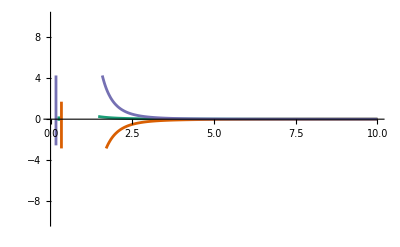

{RGBColor[Rational[9, 85], Rational[158, 255], Rational[7, 15]],RGBColor[Rational[217, 255], Rational[19, 51], Rational[2, 255]],RGBColor[Rational[39, 85], Rational[112, 255], Rational[179, 255]]}

```mathematica
p1=Plot[eigen1[r,0.5,3.8685156556955964],{r,0,10},PlotStyle->colors[[1]]];
p2=Plot[eigen2[r,0.5,3.8685156556955964],{r,0,10},PlotStyle->colors[[2]]];
p3=Plot[eigen3[r,0.5,3.8685156556955964],{r,0,10},PlotStyle->colors[[3]]];
Show[p1,p2,p3,PlotRange->{{0,10},{-10,10}}]
```

```mathematica
p1=Plot[eigen1ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1},PlotStyle->colors[[1]]];
p2=Plot[eigen2ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1},PlotStyle->colors[[2]]];
p3=Plot[eigen3ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1},PlotStyle->colors[[3]]];
p4=Plot[eigensumibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1.1},PlotStyle->{Black,Dashed}];
Show[p1,p2,p3,p4,PlotRange->{{0,1},Automatic},BaseStyle->{FontSize->12},PlotLegends->Placed[{"Lambda1","Lambda2","Lambda3"},{Left,Bottom}],
```

```mathematica
eigen1ibso[r_,Q_]=FullSimplify[eigens[[2]]/.{lz->momentum[r,Q]}]//Factor
eigen2ibso[r_,Q_]=FullSimplify[eigens[[3]]/.{lz->momentum[r,Q]}]//Factor
eigen3ibso[r_,Q_]=FullSimplify[eigens[[4]]/.{lz->momentum[r,Q]}]//Factor
eigensumibso[r_,Q_]=FullSimplify[(eigens[[2]]+eigens[[3]]+eigens[[4]])/.{lz->momentum[r,Q]}]//Factor
```

(-Q^2+r)/r^4

-(Q^4-3 Q^2 r+2 r^2-3 Q^2 r^2+2 r^3)/(r^4 (Q^2-2 r+r^2))

(Q^4-4 Q^2 r+4 r^2-Q^2 r^2+r^3)/(r^4 (Q^2-2 r+r^2))

(Q^2 (-Q^2+2 r+r^2))/(r^4 (Q^2-2 r+r^2))

```mathematica
colors = ResourceFunction["ColorBrewerData"]["Dark2",3]
```

{RGBColor[Rational[9, 85], Rational[158, 255], Rational[7, 15]],RGBColor[Rational[217, 255], Rational[19, 51], Rational[2, 255]],RGBColor[Rational[39, 85], Rational[112, 255], Rational[179, 255]]}

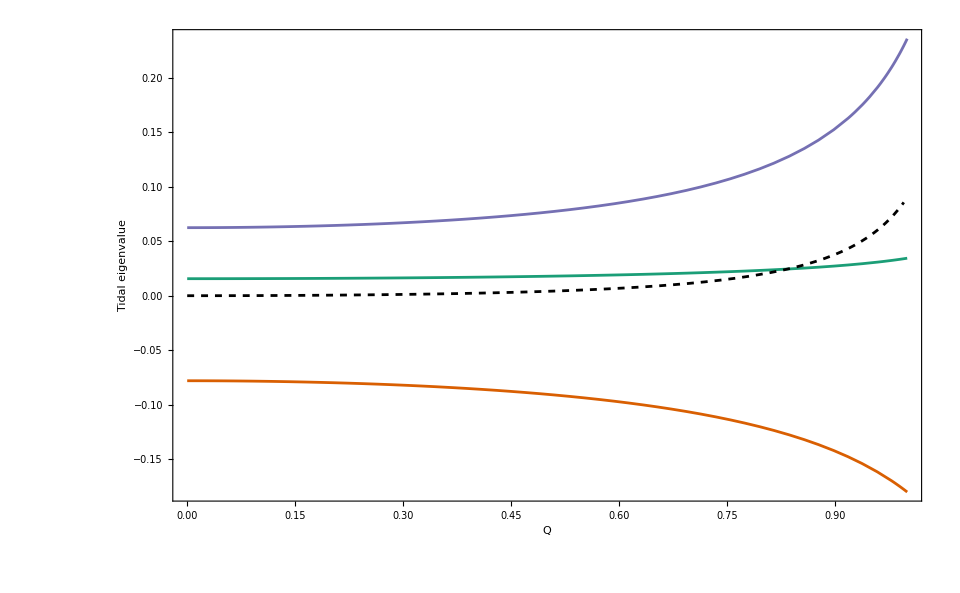

```mathematica
p1=Plot[eigen1ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1},PlotStyle->colors[[1]]];
p2=Plot[eigen2ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1},PlotStyle->colors[[2]]];
p3=Plot[eigen3ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1},PlotStyle->colors[[3]]];
p4=Plot[eigensumibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],{charge,0,1.1},PlotStyle->{Black,Dashed}];
Show[p1,p2,p3,p4,PlotRange->{{0,1},Automatic},BaseStyle->{FontSize->12},PlotLegends->Placed[{"Lambda1","Lambda2","Lambda3"},{Left,Bottom}],FrameLabel->{"Q","Tidal eigenvalue"},Axes->False,Frame->True,FrameStyle->Black,ImageSize->3.2*300,
Epilog->Inset[Framed[Column[{
LineLegend[{colors[[1]]},{Style[ToExpression["\\lambda_{1}",TeXForm,HoldForm]]}],LineLegend[{colors[[2]]},{Style[ToExpression["\\lambda_{2}",TeXForm,HoldForm]]}],LineLegend[{colors[[3]]},{Style[ToExpression["\\lambda_{3}",TeXForm,HoldForm]]}]}],
FrameStyle->None],Scaled[{0.05,0.15}]]]
```

```mathematica
(*Generate list data for plotting in Python*)data=Table[{charge,eigen1ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],eigen2ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],eigen3ibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge],eigensumibso[Max[x/. Solve[expr[x,charge]==0&&x>0,{x},Reals]],charge]},{charge,0,1,0.005}];
Export["eigenibso.dat",data,"Table"]
```

eigenibso.dat